## Computational Mechanics - 2D Forces Intro

### Exercise 2.C3

-Graphics--Graphics-

We know that there is a tension force CA and CB. The only other force is gravity.

```mathematica
fGrav=Quantity[800,"Newtons"];
len=Quantity[20.0,"Meters"];
strlen=Quantity[20.1,"Meters"];
x=Quantity[Table[i,{i,0.5,19.5,0.5}], "Meters"];
```

```mathematica
sol2C3Flat =Table[Flatten[{xi,{y,fAC,fAB}/.Solve[y≤  0&&strlen==√(xi^2+y^2)+√((len-xi)^2+y^2)&&-fGrav ==fAC*(y/(√(xi^2+y^2)))+fAB*(y/(√((len-xi)^2+y^2)))&&fAC*(xi/(√(xi^2+y^2)))== fAB*((len - xi)/(√((len-xi)^2+y^2))),{y,fAC,fAB}]}],{xi,Quantity[0.5,"Meters"],Quantity[19.5,"Meters"],Quantity[0.5,"Meters"]}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

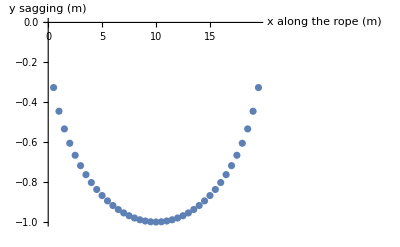

-Graphics-

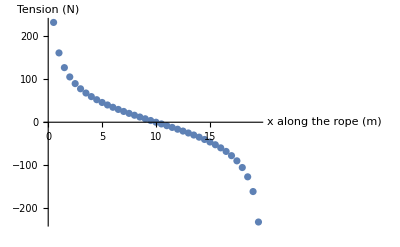

```mathematica
xvals=sol2C3Flat[[1;;,1]];
yvals=sol2C3Flat[[1;;,2]];
fCAvals=sol2C3Flat[[1;;,3]];
fCBvals=sol2C3Flat[[1;;,4]];
ListPlot[Flatten[{xvals,yvals},{{2},{1}}],AxesLabel->{"x along the rope (m)","y sagging (m)"}]

ListPlot[{Flatten[{xvals,fCAvals/Quantity[1,"Newtons"]},{{2},{1}}],Flatten[{xvals,fCBvals/Quantity[1,"Newtons"]},{{2},{1}}]},AxesLabel->{"x along the rope (m)","Tension (N)"},PlotLabels->{"Tension CA", "Tension CB"}]
ListPlot[Flatten[{xvals,(fCAvals-fCBvals)/Quantity[1,"Newtons"]},{{2},{1}}],AxesLabel->{"x along the rope (m)","Tension (N)"}]
```

### Exercise 3.C4

-Graphics--Graphics-

```mathematica
hoseDiam=UnitConvert[Quantity[50,"Millimeters"],"Meters"];
hoseLen=Quantity[30,"Meters"];
spoolDiam=Quantity[0.6,"Meters"];
spoolWidthWound=Quantity[250,"Millimeters"];
numRevs=spoolWidthWound/hoseDiam;
xGivenRev[diam_,rev_]:=π*diam*rev
StringForm["There are { `` } Revolutions per width of the spool: ``",numRevs, spoolWidthWound]

fSpool[x_]:=Quantity[300(1-x/hoseLen),"Newtons"]
momentSpool[x_]:=fSpool[x]*(hoseDiam+spoolDiam)/2
momentSpool[Quantity[0,"Meters"]]
momentSpool[hoseLen]
```

There are { 5 } Revolutions per width of the spool: 250

97.5 m N

0. m N

We first run a simple model assuming at the spool is only wound one time.

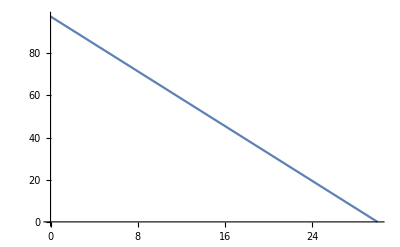

{0. m,2.04204 m,4.08407 m,6.12611 m,8.16814 m,10.2102 m}

{97.5 m N,90.8634 m N,84.2268 m N,77.5902 m N,70.9535 m N,64.3169 m N}

```mathematica
Plot[momentSpool[Quantity[x,"Meters"]],{x,0,hoseLen/Quantity["Meters"]}]
Table[xGivenRev[spoolDiam+hoseDiam,i],{i,0,5,1}]
Table[momentSpool[xGivenRev[spoolDiam+hoseDiam,i]],{i,0,5,1}]
```

However, the width of the spool is not long enough for one wound.

```mathematica
firstWoundHoseLen=xGivenRev[spoolDiam+hoseDiam/2,numRevs]
secondWoundHoseLen=xGivenRev[spoolDiam+hoseDiam,numRevs]
Sum[xGivenRev[spoolDiam+i*hoseDiam/2,numRevs],{i,0,2}]
```

9.81748 m

10.2102 m

29.4524 m

It takes about two wounds. Each wound has an increase in radius given by the diameter of the hose.

0.325 m

0.35 m

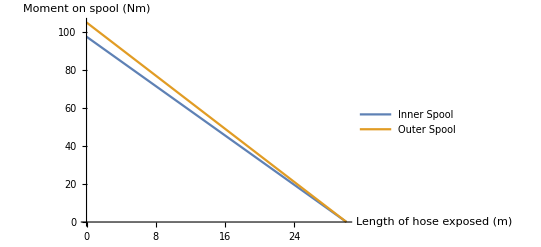

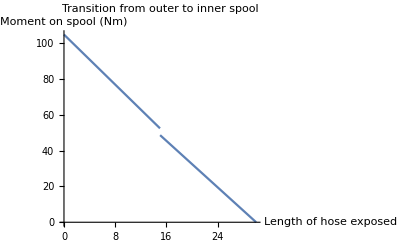

```mathematica
momentSpoolGen[x_,rad_]:=fSpool[x]*rad
rad1=(spoolDiam+hoseDiam)/2
rad2=(spoolDiam+2*hoseDiam)/2
Plot[{momentSpoolGen[Quantity[x,"Meters"],rad1],momentSpoolGen[Quantity[x,"Meters"],rad2]},{x,0,hoseLen/Quantity["Meters"]},PlotLegends->{"Inner Spool","Outer Spool"},AxesLabel->{"Length of hose exposed (m)","Moment on spool (Nm)"}]
Plot[Piecewise[{{momentSpoolGen[Quantity[x,"Meters"],rad2],x<hoseLen/(2*Quantity["Meters"])},{momentSpoolGen[Quantity[x,"Meters"],rad1],x>hoseLen/(2*Quantity["Meters"])}}],{x,0,hoseLen/Quantity["Meters"]},PlotLabel->"Transition from outer to inner spool",AxesLabel->{"Length of hose exposed (m)","Moment on spool (Nm)"}]
```

### Exercise 3.C5

We want to develop a program that given any combination of forces and location, we can find the equivalent force couple at that point.

Input
(pX,pY,pZ) - The coordinates of the point in question
Table of the forces in the form [Mag, (dx, dy, dz),(cx,cy,cz)] where Mag is the magnitude, (dx, dy, dx) represents the unit direction vector, and (cx, cy,cz) represents the coordinate at which it acts

Output
(mX, mY, mZ) - Moment at the point in question
(fOutX, fOutY, fOutZ) - Force at the point in question

For the sake of trying out the math first...

```mathematica
f1={10,Normalize[{4,5,3}],{2,3,4}};
f2={5,Normalize[{7,2,1}],{5,-3,4}};
f3={6,Normalize[{8,9,4}],{-2,3,-4}};
f1 [[2]]// MatrixForm;
f1[[1]]*f1[[2]];
fNet=f1[[1]]*f1[[2]]+f2[[1]]*f2[[2]]+f3[[1]]*f3[[2]];
N[fNet]

p1={2,-3,4};
radVec1=f1[[3]]-p1;
mom1=(radVec1×f1[[2]])*f1[[1]];
radVec2=f2[[3]]-p1;
mom2=(radVec2×f2[[2]])*f2[[1]];
radVec3=f3[[3]]-p1;
mom3=(radVec3×f3[[2]])*f3[[1]];
N[mom1+mom2+mom3]
```

{14.2027,12.6877,6.81452}

{70.851,-24.7388,-69.5794}

Now for the actual fun.  “g” sands for general.

```mathematica
pg={px,py,pz};
f1g={magF1,{fdx1,fdy1,fdz1},{cx1,cy1,cz1}};
f2g={magF2,{fdx2,fdy2,fdz2},{cx2,cy2,cz2}};
f3g={magF3,{fdx3,fdy3,fdz3},{cx3,cy3,cz3}};

pQuestion={2,-3,4}
f12={10,Normalize[{4,5,3}],{2,3,4}};
f22={5,Normalize[{7,2,1}],{5,-3,4}};
f32={6,Normalize[{8,9,4}],{-2,3,-4}};

forceList={f12,f22,f32};
numForces=3;
forceNet=Sum[forceList[[i]][[1]]*forceList[[i]][[2]],{i,1,numForces}];
momentNet=Sum[forceList[[i]][[1]]*((forceList[[i]][[3]]-pQuestion)×forceList[[i]][[2]]),{i,1,numForces}];

StringForm["
The net force at `` is ``.
The net moment at `` is ``.",p1//MatrixForm,N[forceNet]//MatrixForm,p1//MatrixForm,N[momentNet]//MatrixForm]
```

{2,-3,4}

The net force at (2
-3
4) is (14.2027
12.6877
6.81452).
The net moment at (2
-3
4) is (70.851
-24.7388
-69.5794).